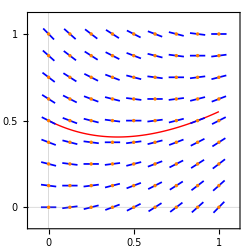

/Users/maba/Documents/hs-bochum/05-numMat/01-skript/__a-01-eine-unbekannte-funktion/00-pics/beispiel-dgl.pdf

```mathematica
plot[s_,pps_:True,a1_:1/2,a2_:1/8]:=Module[
{slope, l, phi, dx, dy,f1,f2,p1,p2}
,
f1=Quiet[y[x]/.NDSolve[{y'[x]==(s/.y->y[x]),y[0]==a1},y[x],{x,0,1}]//First];

p1=Plot[{f1},{x,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[{Thick,Red}],PlotTheme->"Scientific",FrameTicks->{{{0,0.5,1},{}},{{0,0.5,1},{}}},AspectRatio->Automatic,ImageSize->250];
p2=Graphics[
{
Table[
slope=s/.{x->xx,y->yy};
slope=If[NumberQ[slope],slope,10000];
l=0.045;
phi=ArcTan[slope];
dx=Cos[phi]*l;
dy=Sin[phi]*l;
{
Blue,AbsoluteThickness[1.25]
,
Line[{{xx-dx,yy-dy},{xx+dx,yy+dy}}]
,
{
Directive[Orange]
,
Disk[{xx,yy},0.01]
}
}
,
{xx,0,1,0.125}
,
{yy,0,1,0.125}
]
}
];

If[
pps,
Show[{p1,p2},PlotRange->{{-0.1,1.1},{-0.1,1.1}}],
Show[{p2},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]
]
]

p=plot[x-y,True,1/2]
Export[NotebookDirectory[]<>"beispiel-dgl.pdf",p]
```